## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="TPI";
fitLabel="p1";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_TPI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/TPI/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{g3p,Null,Keq substrate}

{9.35,Keq value}

{g3p,Km or S05 substrate}

{0.00103,Km or S05 value}

{{{g3p,Null}},kcat substrates}

{9000,kcat value}

{2-phosphoglycolate,Inhibition or activation constant substrate}

{0.006,Inhibition or activation constant value}

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1}(*{10}*);
s05Priorities = Null;
kcatPriorities = {1}(*{0.0001}*);
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities =Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### mechanism

```mathematica
catalyticBranch={"E_TPI[c] + g3p[c] <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TPI^c)_^+g3p^c⇌(TPI^c&g3p^c)_^)^TPI1,((TPI^c&dhap^c)_^⇌(TPI^c)_^+dhap^c)^TPI2,((TPI^c&g3p^c)_^⇌(TPI^c&dhap^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{g3p^c→0}

{dhap^c→0}

{g3p^c→∞}

{dhap^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
rxn
```

(dhap^c⇌g3p^c)^TPI

```mathematica
enzymeModel["Reactions"]
```

{((TPI^c)_^+g3p^c⇌(TPI^c&g3p^c)_^)^TPI1,((TPI^c&dhap^c)_^⇌(TPI^c)_^+dhap^c)^TPI2,((TPI^c&g3p^c)_^⇌(TPI^c&dhap^c)_^)^TPI3}

```mathematica
absoluteRateForward//Simplify
```

(g3p^c TPI_total_Global k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+g3p^c k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶))

```mathematica
relativeRateForward//Simplify
```

{(g3p^c k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶))/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+g3p^c k_TPI1^⟶ (k_TPI2^⟶+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
haldaneRatiosList
```

{(k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)}

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/haldaneRatio_1.txt"	9.35
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/relRateFor_g3p.txt"	0.9090909090909091
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207
1	0	0.01	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/input/absRateFor.txt"	27025.299764582207

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.984412529306
best_fit: 0.883973749734
best_fit: 0.706168361531
best_fit: 0.727728816705
best_fit: 0.943382106692
best_fit: 0.971684322163
best_fit: 0.937785995973
best_fit: 0.43689385924
best_fit: 0.182901173906
best_fit: 0.775459238089
best_fit: 1.08306288302
best_fit: 0.797013649234
best_fit: 0.579716538383
best_fit: 0.256102463388
best_fit: 0.917480677839
best_fit: 0.951541079286
best_fit: 1.02370391037
best_fit: 1.07198511031
best_fit: 0.583279551737
best_fit: 0.632347728563
best_fit: 0.737694459078
best_fit: 1.02513265391
best_fit: 0.725317999837
best_fit: 0.801357675645
best_fit: 1.09961672838
best_fit: 1.01238018622
best_fit: 0.140383473358
best_fit: 0.821620332507
best_fit: 0.72139200628
best_fit: 0.428917646718
best_fit: 0.815988506939
best_fit: 1.07301644474
best_fit: 0.236101493038
best_fit: 0.97261973899
best_fit: 0.713444875326
best_fit: 0.887028502914
best_fit: 0.711014790815
best_fit: 0.951674588064
best_fit: 0.650234400651
best_fit: 0.463033082415
best_fit: 0.887360164801
best_fit: 0.998302833684
best_fit: 0.960485798244
best_fit: 1.03379693158
best_fit: 0.335688715288
best_fit: 0.717968109552
best_fit: 0.791007035708
best_fit: 0.501077322154
best_fit: 0.661430148901
best_fit: 0.844695889288
best_fit: 0.880464967312
best_fit: 0.388333249459
best_fit: 0.975650355344
best_fit: 1.02375743312
best_fit: 0.970397377322
best_fit: 0.427774965544
best_fit: 0.92824887915
best_fit: 1.04808446712
best_fit: 0.664289474106
best_fit: 1.0996133093
best_fit: 0.99849690211
best_fit: 0.765332995767
best_fit: 0.90189465451
best_fit: 1.04479881927
best_fit: 0.610161551687
best_fit: 0.66788635478
best_fit: 1.03996651016
best_fit: 0.866190341992
best_fit: 0.987541316956
best_fit: 0.613705222847
best_fit: 0.820188217748
best_fit: 0.892930459064
best_fit: 0.502149845689
best_fit: 0.474952230705
best_fit: 1.08603511234
best_fit: 0.920055670499
best_fit: 0.808400860714
best_fit: 0.850593104885
best_fit: 1.0753302413
best_fit: 0.773601327667
best_fit: 0.59398230303
best_fit: 0.492011017664
best_fit: 0.548317680357
best_fit: 0.647178355952
best_fit: 0.818997439287
best_fit: 1.00343252247
best_fit: 0.620942940326
best_fit: 0.42154494805
best_fit: 0.93498906624
best_fit: 0.7733000773
best_fit: 0.433069344382
best_fit: 0.995552538851
best_fit: 0.456923436671
best_fit: 0.989400192684
best_fit: 0.71761253
best_fit: 0.774960308727
best_fit: 0.763819892905
best_fit: 0.853383322912
best_fit: 0.519040176003
best_fit: 0.781203697866

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=
"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/output/raw/lmaResults_p1_20181191029.txt";
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_1"];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.51899×10^-12 | 6.34529×10^-24 | 5.42304×10^-11 | 5.80004×10^-10 | 9.35 | 9.35
1 | relRateFor_g3p | 3.25695×10^-12 | 1.06077×10^-23 | 6.81774×10^-13 | 7.49951×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_g3p | 3.09242×10^-12 | 9.56303×10^-24 | 9.74137×10^-13 | 7.12053×10^-10 | 0.136807 | 0.136807
1 | relRateFor_g3p | 2.86338×10^-12 | 8.19892×10^-24 | 1.32364×10^-12 | 6.59312×10^-10 | 0.20076 | 0.20076
1 | relRateFor_g3p | 2.56262×10^-12 | 6.567×10^-24 | 1.68016×10^-12 | 5.90052×10^-10 | 0.284747 | 0.284747
1 | relRateFor_g3p | 2.19669×10^-12 | 4.82543×10^-24 | 1.95682×10^-12 | 5.05818×10^-10 | 0.386863 | 0.386863
1 | relRateFor_g3p | 1.79134×10^-12 | 3.20892×10^-24 | 2.06235×10^-12 | 4.1247×10^-10 | 0.5 | 0.5
1 | relRateFor_g3p | 1.386×10^-12 | 1.921×10^-24 | 1.95677×10^-12 | 3.19141×10^-10 | 0.613137 | 0.613137
1 | relRateFor_g3p | 1.02021×10^-12 | 1.04083×10^-24 | 1.68021×10^-12 | 2.34912×10^-10 | 0.715253 | 0.715253
1 | relRateFor_g3p | 7.19286×10^-13 | 5.17372×10^-25 | 1.32372×10^-12 | 1.65622×10^-10 | 0.79924 | 0.79924
1 | relRateFor_g3p | 4.90163×10^-13 | 2.4026×10^-25 | 9.74221×10^-13 | 1.12862×10^-10 | 0.863193 | 0.863193
1 | relRateFor_g3p | 3.25767×10^-13 | 1.06124×10^-25 | 6.81899×10^-13 | 7.50089×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3
1 | absRateFor | 8.26006×10^-14 | 6.82286×10^-27 | 5.13683×10^-9 | 1.90075×10^-11 | 27025.3 | 27025.3

### Simulated Data and Best Fit Data Plot

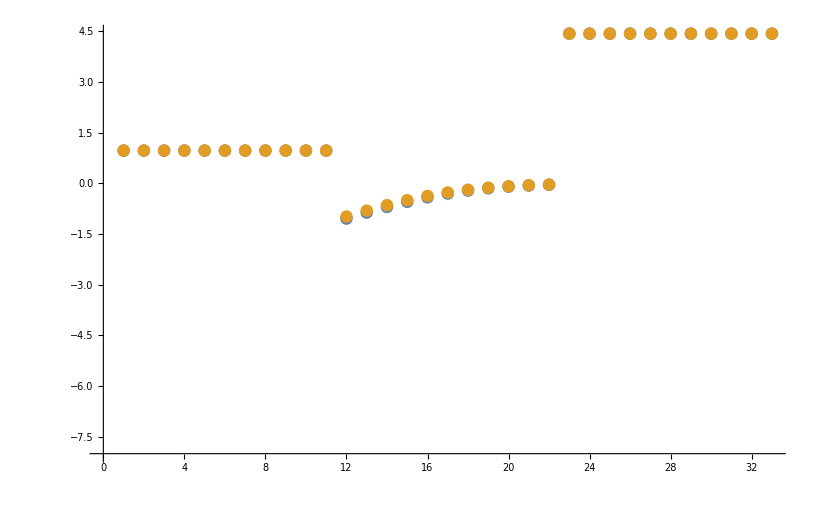

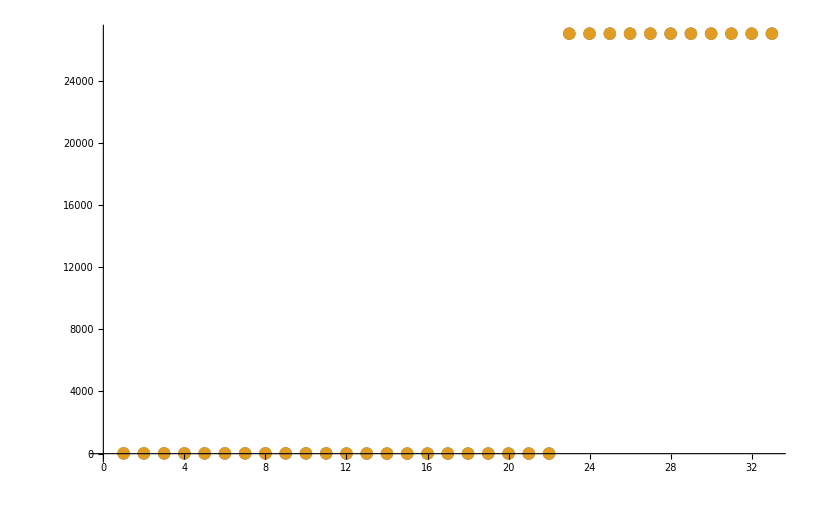

```mathematica
datasetI=40;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

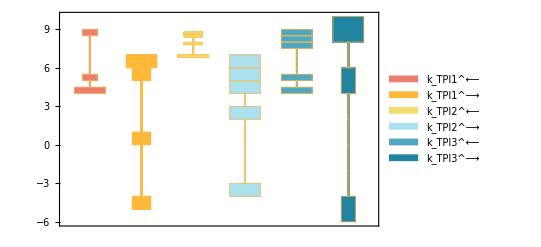

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

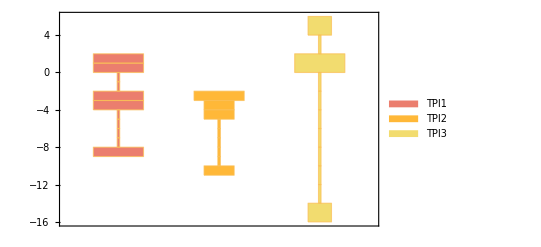

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

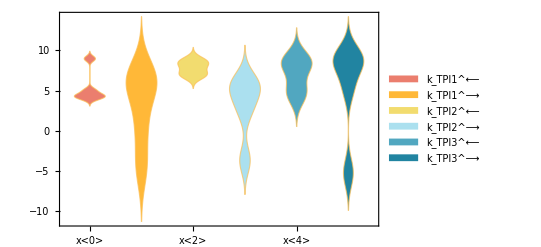

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

{1,1}

{g3p^c→∞}

g3p^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→0.00103}}

data value | predicted value | error in %
0.00103 | 0.00103 | 1.84487×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
27025.3 | 27025.3 | 0.0000226811

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
9.35 | 9.35 | 8.24153×10^-6

#### Export rate back calculated parameter error distribution

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
nRateSets=100;
predictedParamsErrorList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_1.csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

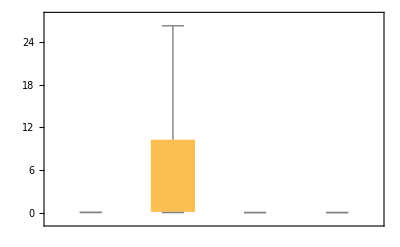

```mathematica
BoxWhiskerChart[Transpose@predictedParamsErrorList[[3;;50,All]]]
```

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```